```mathematica
(*price
produktionskvantitet
maskin (ja/nej)
*)


unitsPerYear = 80000
annualRevenue = 1.3*10^6
marginalLoss=40000
machineCost = 450000
varCostOriginal=5
varCostWithMachine=3
```

```mathematica
data = {
{2014,10300,15},
{2015,8100,17},
{2016,7400,18}
};

sub1 = data[[All,2;;3]]
```

{{10300,15},{8100,17},{7400,18}}

{{2014,154500},{2015,137700},{2016,133200}}

39.3086-0.00420511 x+1.79131×10^-7 x^2

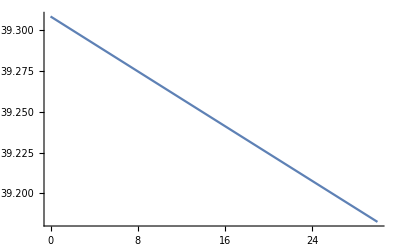

```mathematica
localrevdata = {
{2014,10300*15},
{2015,8100*17},
{2016,7400*18}
}

unitssold=Fit[{{10300,15},{8100,17},{7400,18}},{1,x,x^2},x]

Show[
Plot[Function[unitssold][x], {x, 0,30}],
ListPlot[{{10300,15},{8100,17},{7400,18}}, PlotStyle->Red]
]
```

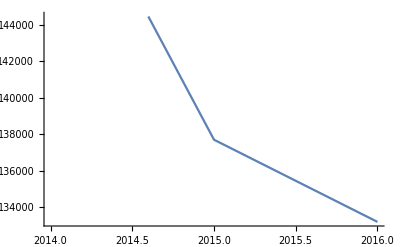

```mathematica
ListPlot[localrevdata,Joined->True]
```

```mathematica
Show[
ListPlot[sub1, Joined->True]
]
```

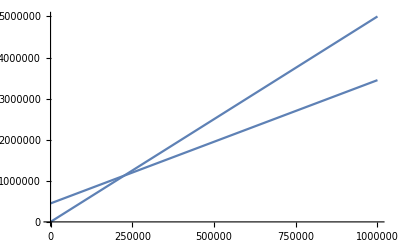

{{x→225000}}

```mathematica
withoutMachine = Function[x,5x];
withMachine=Function[x,3x+450000];

Show[
Plot[withoutMachine[x],{x,0,1000000}],
Plot[withMachine[x],{x,0,1000000}]
]

Solve[withMachine[x]==withoutMachine[x],x]
```

```mathematica
N[1300000/18]
```

72222.2